```mathematica
u1[z1_, q_] = Sqrt[q]*z1
u2[z1_, z2_, cPrev_, q_] = Sqrt[q]*(cPrev*z1 + Sqrt[1 - cPrev^2]*z2)
phi[x_] = Max[0,x]
normalDistr[z_] = (1/Sqrt[2*Pi])*E^((-z^2)/2)
```

√q z1

√q (cPrev z1+√(1-cPrev^2) z2)

Max[0,x]

(ⅇ^(-z^2/2))/(√(2 π))

```mathematica
Integrate[Integrate[phi[u1[z1, paRqAAStar]]*phi[u2[z1, z2, paRcPrev, paRqAAStar]]*normalDistr[z1] * normalDistr[z2], z2], z1]
```

Piecewise[{{(paRqAAStar (2 ⅇ^(-z1^2/2-z2^2/2) √(1-paRcPrev^2)+(-ⅇ^(-z1^2/2) paRcPrev √(2 π) z1+paRcPrev π Erf[z1/(√2)]) Erf[z2/(√2)]))/(4 π), √paRqAAStar z1>0&&paRcPrev √paRqAAStar z1+√(1-paRcPrev^2) √paRqAAStar z2>0}, {0, True}}]

```mathematica
NIntegrate[NIntegrate[phi[u1[z1, 2]]*phi[u2[z1, z2, 0.8, 2]]*normalDistr[z1] * normalDistr[z2], {z2, -10, 10}], {z1, -10, 10}]
```

NIntegrate::inumr: The integrand (ⅇ^(-z1^2/2-z2^2/2) Max[0,√2 z1] Max[0,√2 (0.8 z1+0.6 z2)])/(2 π) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-10,10}}.

NIntegrate::inumr: The integrand (ⅇ^(-z1^2/2-z2^2/2) Max[0,-√2 z1] Max[0,√2 (-0.8 z1+0.6 z2)])/(2 π) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-10,10}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

0.82712

```mathematica
Integrate[Integrate[phi[u1[z1, paRqAAStar]]*phi[u2[z1, z2, paRcPrev, paRqAAStar]]*normalDistr[z1] * normalDistr[z2], {z2, -Infinity, Infinity}], {z1, -Infinity, Infinity}]
```

Piecewise[{{paRqAAStar/2, paRqAAStar>0&&paRcPrev==1}, {1/(2 π)paRqAAStar (√(1-paRcPrev^2)+paRcPrev π+ⅈ paRcPrev ArcCosh[paRcPrev]), paRqAAStar>0&&0<paRcPrev<1}, {1/(4 π)paRqAAStar (2 √(1-paRcPrev^2)+paRcPrev π+2 paRcPrev ArcSin[paRcPrev]), paRqAAStar>0&&-1<paRcPrev≤0}, {0, True}}]

```mathematica
Integrate[Integrate[phi[u1[z1, 2]]*phi[u2[z1, z2, 0.8, 2]]*normalDistr[z1] * normalDistr[z2], {z2, -Infinity, Infinity}], {z1, -Infinity, Infinity}]
```

0.82712

```mathematica
(2 (√(1-0.8^2)+0.8 π+ⅈ *0.8* ArcCosh[0.8]))/(2 π)
```

0.82712+0. ⅈ

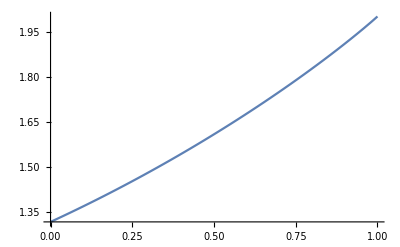

```mathematica
Plot[(2* (√(1-paRcPrev^2)+paRcPrev π+ⅈ paRcPrev ArcCosh[paRcPrev]))/(2 π)+1,{paRcPrev, 0, 1}]
```

```mathematica
ArcCosh[0.8]
```

0.+0.643501 ⅈ

```mathematica
Piecewise[{{paRqAAStar/2, paRqAAStar>0&&paRcPrev==1}, {1/(2 π)paRqAAStar (√(1-paRcPrev^2)+paRcPrev π+ⅈ paRcPrev ArcCosh[paRcPrev]), paRqAAStar>0&&0<paRcPrev<1}, {1/(4 π)paRqAAStar (2 √(1-paRcPrev^2)+paRcPrev π+2 paRcPrev ArcSin[paRcPrev]), paRqAAStar>0&&-1<paRcPrev≤0}, {0, True}}]
```